## Input

## State object

```mathematica
ClearAll[State]
Protect[State]
```

{State}

### Getters

```mathematica
BBox[State[bbox_,samples_,mask_]]:=bbox;
Samples[State[bbox_,samples_,mask_]]:=samples;
CorrectMask[State[bbox_,samples_,mask_]]:=mask;
```

### Setter

Check that a sample in a box

```mathematica
InClosedBoxQ[sample_,bbox_]:=And@@MapThread[(#2⟦1⟧-#1≤0)&&(0≤#2⟦2⟧-#1)&,{sample,bbox}]
InOpenBoxQ[sample_,bbox_]:=And@@MapThread[(#2⟦1⟧-#1<0)&&(0<#2⟦2⟧-#1)&,{sample,bbox}]
```

```mathematica
SetBBox[state_,bbox_]:=State[bbox,Pick[Samples[state],#],Pick[CorrectMask[state],#]]&[Map[InOpenBoxQ[#,bbox]&,Samples[state]]]
```

### Member functions

```mathematica
CorrectSamples[State[bbox_,samples_,mask_]]:=Pick[samples,mask];
IncorrectSamples[State[bbox_,samples_,mask_]]:=Pick[samples,mask,False];
```

```mathematica
OpenBoxMask[state_State]:=Map[InOpenBoxQ[#,BBox[state]]&,Samples[state]]
```

## Find inner or outer bounding box

Bounding box is a list of pairs. Every pair consists of limits {min, max} for every parameter

```mathematica
FindInnerBox[state_State]:=
MapThread[
{Max[#1⟦1⟧,#2⟦1⟧],Min[#1⟦2⟧,#2⟦2⟧]}&,
{
BBox[state],
{Min[#],Max[#]}&/@Transpose@CorrectSamples[state]
}];
```

```mathematica
MaxFromList[list_,default_]:=If[Length[list]==0,default,Max[list]]
MinFromList[list_,default_]:=If[Length[list]==0,default,Min[list]]
```

```mathematica
FindOuterBox[state_State]:=
If[
And@@CorrectMask[state],
BBox[state],
MapThread[
Function[
{
paramSamples,
inLimits,
outLimits
},
{
MaxFromList[Select[paramSamples,#<inLimits⟦1⟧&],outLimits⟦1⟧],
MinFromList[Select[paramSamples,#>inLimits⟦2⟧&],outLimits⟦2⟧]
}],
{Transpose@IncorrectSamples[state],FindInnerBox[state],BBox[state]}
]
]
```

## Recall

Find ration of correct/total in bounding box

```mathematica
FindRecall[state_State]:=
Module[
{
inBoxMask=OpenBoxMask[state]
},
N@Count[MapThread[And,{inBoxMask,CorrectMask[state]}],True]/Count[inBoxMask,True]
]
```

## Split bounding box

```mathematica
ClearAll[FindSplittingThreshold,SplitBBox]
```

```mathematica
FindSplittingThreshold[state_State,idx_]:=
Module[
{
inBoxMask=OpenBoxMask[state],
values
},
values=Map[#⟦idx⟧&,Pick[Samples[state],inBoxMask]];
FindThreshold[Pick[values,Pick[CorrectMask[state],inBoxMask]]]
]
```

```mathematica
SplitBBox[bbox_,threshold_,idx_]:=
{
ReplacePart[bbox,idx->{bbox⟦idx,1⟧,threshold}],
ReplacePart[bbox,idx->{threshold,bbox⟦idx,2⟧}]
}
```

## Refine and split state

In that follows we ignore subnormal floating point numbers

```mathematica
ClearAll[NextAfter,NextBefore]
NextAfter[0.]=$MinMachineNumber;
NextAfter[x_]/;Precision[x]==MachinePrecision:=With[{me=MantissaExponent[x,2]},(2First[me]+$MachineEpsilon)Power[2,Last[me]-1]]

NextBefore[0.]=-$MinMachineNumber;
NextBefore[x_]/;Precision[x]==MachinePrecision:=With[{me=MantissaExponent[x,2]},(2First[me]-$MachineEpsilon)Power[2,Last[me]-1]]
```

```mathematica
ClearAll[RefineState]
RefineState=Function[{state},SetBBox[state,FindOuterBox[state]]];
```

```mathematica
ClearAll[CloseBBox]
CloseBBox[bbox_]:=Map[{NextBefore[#⟦1⟧],NextAfter[#⟦2⟧]}&,bbox]

ClearAll[SplitState]
SplitState=
Function[{state,splitIndex},
If[
And@@CorrectMask[state],
{state},
Module[
{
splitBoxes=SplitBBox[BBox[state],FindSplittingThreshold[state,splitIndex],splitIndex]
},
{
RefineState@SetBBox[state,CloseBBox[splitBoxes⟦1⟧]],
RefineState@SetBBox[state,splitBoxes⟦2⟧]
}
]
]
];
```

## Picture

```mathematica
colors=ColorData[94,"ColorList"];
```

```mathematica
PlotState[state_State]:=
Module[
{
outBox=FindOuterBox[state]
},
Graphics[
{
{FaceForm[Directive[colors⟦1⟧,Opacity[0.25]]],EdgeForm[None],Rectangle@@Transpose[outBox]},
{FaceForm[None],EdgeForm[colors⟦1⟧],Rectangle@@Transpose[BBox[state]]},
{Orange,PointSize-> Medium,Point@CorrectSamples[state]},
{Blue,PointSize-> Medium,Point@IncorrectSamples[state]}
}
]
]
```

```mathematica
PlotStates[states_,samples_,mask_]:=
Graphics[
Join[
Table[
{FaceForm[Directive[colors⟦1⟧,Opacity[0.25]]],EdgeForm[colors⟦1⟧],Rectangle@@Transpose[BBox[s]]},
{s,states}],
{
{Orange,PointSize-> Medium,Point[Pick[samples,mask]]},
{Blue,PointSize-> Medium,Point[Pick[samples,mask,False]]}
}
]
]
```

## Output

## Demo bounding box refinement

### Data

Objective function

```mathematica
f[x_,y_]:=4(x^2+y^2)(1-(x^2+y^2));
```

```mathematica
GetSamples[n_]:=Sqrt[#1]{Cos[2π #2],Sin[2π #2]}&@@@RandomReal[{0,1},{n,2}]
samples=GetSamples[288];
weights=f@@@samples;
mask=Thread[weights≥0.8];
```

### Bounding boxes

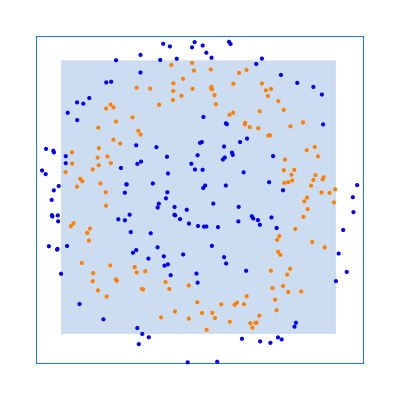

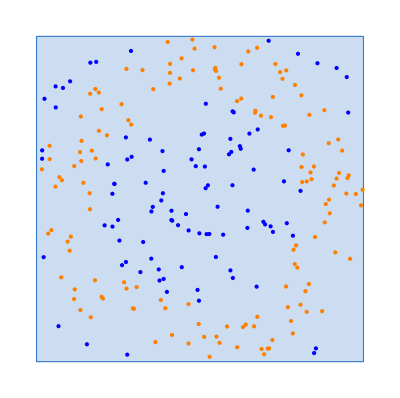

{0.589212}

```mathematica
states={State[{{-1,1},{-1,1}},samples,mask]};
Show[PlotState/@states]
states=RefineState/@states;
Show[PlotState/@states]
FindRecall/@states
```

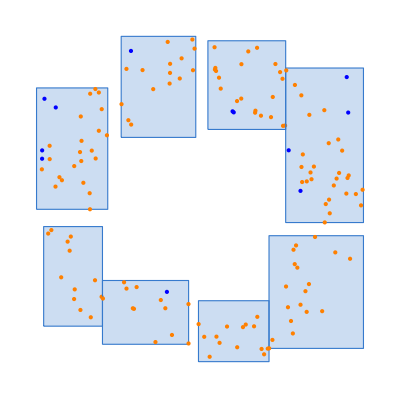

{1.,0.923077,0.846154,0.9375,1.,1.,0.913043,0.875}

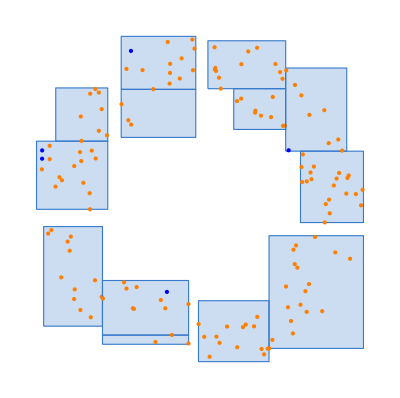

{1.,1.,0.909091,0.875,1.,1.,0.923077,1.,1.,1.,1.,1.,0.888889}

```mathematica
states=Join@@(SplitState[#,1]&/@states);
Show[PlotState/@states]
FindRecall/@states

states=Join@@(SplitState[#,2]&/@states);
Show[PlotState/@states]
FindRecall/@states
```

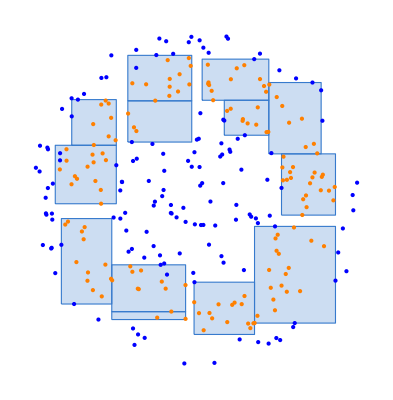

```mathematica
PlotStates[states,samples,mask]
```